```mathematica
CellularAutomaton[{{a,_,b}->a,{b,_,a}->b,{a,_,a}->a},{a,a,a,b,a},4] (*How CellularAutomaton func works*)
```

{{a,a,a,b,a},{a,a,a,a,b},{b,a,a,a,a},{a,b,a,a,a},{a,a,b,a,a}}

```mathematica
{$,_,_,_,_,_,$} (*The layout of the state of the automaton boundary conditions are fixed*)
```

```mathematica
MaxRodRules[n_]:=2^4 2^(2^(n-2))2^4 (*Find the number of possible rules that can be applied given the structure of the 1D robot*)
```

2^4 : {fixed, 1/0, 1/0}  4 “blocks” that can each take one of two values
(2^(n-2))
2^4 : {1/0, 1/0, fixed} therefore 2^2*2^2 = 2^4

```mathematica
MaxRodStates[n_]:=4+2^(n-2)+4  (* 2^n *)
```

```mathematica
{{$,s,s},{$,s,l},{$,l,s},{$,l,l},{s,s,s},{s,s,l},...,}
```

```mathematica
IntegerDigits[324,2] (*An integer in base 2 notation*)
```

{1,0,1,0,0,0,1,0,0}

```mathematica
2^2 + 2^6 + 2^8
```

324

```mathematica
IntegerDigits[RandomInteger@MaxRodRules[5]-1,2] (*-1 to start numbering from zero for the possible rules, one possible rule*)
```

{1,0,1,1,1,0,0,1,1,1,0,0,1,0,0}

```mathematica
MaxRodRules@5 (*For 5 rods in the mechanism, how many possible rules can we have?*)
```

65536

```mathematica
Tuples[{0,1},3](*for the states 1 and 0, how may different configs can we have for a list of length 3 (neigbours and self)*)
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
Join[Prepend[2]/@Tuples[{0,1},2],Tuples[{0,1},3],Append[2]/@Tuples[{0,1},2]] (*All the possible scenarios we could encounter and would then apply a rule to*)
(*This is dependent on the structure of the mechanism but independent of the number of rods in the mechanism*) 
(*16 in this case*)
```

{{2,0,0},{2,0,1},{2,1,0},{2,1,1},{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{0,0,2},{0,1,2},{1,0,2},{1,1,2}}

```mathematica
ClearAll@ToRodRule; (*Clear this definition so that it does not mess with you in the future*)
ToRodRule[rule_]:=Join[MapThread[Rule,{Join[Prepend[2]/@Tuples[{0,1},2],Tuples[{0,1},3],Append[2]/@Tuples[{0,1},2]],IntegerDigits[rule-1,2,16]}],{{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2}]
```

```mathematica
RodEvolution[rule_,n_,t_,init_:Automatic]:=CellularAutomaton[ToRodRule[rule],Replace[init,Automatic->Join[{2},ConstantArray[0,n],{2}]],t]
```

```mathematica
RodEvolution[12,5,10](*What will the evolution of states be for rule 12, 5 rods and 10 timesteps?*)
```

{{2,0,0,0,0,0,2},{2,0,0,0,0,1,2},{2,0,0,0,0,0,2},{2,0,0,0,0,1,2},{2,0,0,0,0,0,2},{2,0,0,0,0,1,2},{2,0,0,0,0,0,2},{2,0,0,0,0,1,2},{2,0,0,0,0,0,2},{2,0,0,0,0,1,2},{2,0,0,0,0,0,2}}

```mathematica
FindRepeat  (*Performace metrics for a given rule*)
FindTransientRepeat
```

```mathematica
Table[ArrayPlot[RodEvolution[rule,20,100],PlotLabel->rule],{rule,RandomInteger[2^16,30]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
interesting={38319,55183,34667,50845,34670};
```

```mathematica
ArrayPlot/@Partition[RodEvolution[38319,20,500],100] (*Plot interesting ca that is long*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rule@@@Partition[Range@10,2,1] (*Map each state that existed to the following state it would go to*)
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10}

```mathematica
Column[FromDigits[#1]->FromDigits[#2]&@@@Partition[RodEvolution[10,20,6],2,1]](*Map each state that existed to the following state it would go to*)
```

2000000000000000000002→2000000000000000000012
2000000000000000000012→2000000000000000000002
2000000000000000000002→2000000000000000000012
2000000000000000000012→2000000000000000000002
2000000000000000000002→2000000000000000000012
2000000000000000000012→2000000000000000000002

Plot the transition diagrams for some of the selected interesting rules

```mathematica
Table[With[{evol=RodEvolution[rule,20,100]},FlipView[{Graph[Union[Rule@@@Partition[evol,2,1]]],ArrayPlot[evol,PlotLabel->rule]}]],{rule,interesting}]
```

{,,,,}

{{0,0,0,0,0,0,0,0,0,0,0,0},{0,1.5,0,0,0,0,0,0,0,0,1.5,0},{0,0,1.5,0,0,0,0,0,0,1.5,1.5,0},{0,1.5,1.5,1.5,0,0,0,0,1.5,0,0,0},{0,0,1.5,0,1.5,0,0,1.5,1.5,1.5,1.5,0},9991,{0,0,0,0,0,0,0,0,1.5,0,1.5,0},{0,1.5,0,0,0,0,0,1.5,1.5,0,1.5,0},{0,0,1.5,0,0,0,1.5,0,0,0,1.5,0},{0,1.5,1.5,1.5,0,1.5,1.5,1.5,0,1.5,1.5,0},{0,0,1.5,0,0,0,1.5,0,0,0,0,0}}
 |  |  |  |

{{0,0,0,0,0,0,0,0,0,0},{1.5,0,0,0,0,0,0,0,0,1.5},{0,1.5,0,0,0,0,0,0,1.5,1.5},{1.5,1.5,1.5,0,0,0,0,1.5,0,0},{0,1.5,0,1.5,0,0,1.5,1.5,1.5,1.5},{1.5,1.5,0,1.5,1.5,1.5,0,1.5,1.5,0},9990,{0,0,0,0,0,0,0,1.5,0,1.5},{1.5,0,0,0,0,0,1.5,1.5,0,1.5},{0,1.5,0,0,0,1.5,0,0,0,1.5},{1.5,1.5,1.5,0,1.5,1.5,1.5,0,1.5,1.5},{0,1.5,0,0,0,1.5,0,0,0,0}}
 |  |  |  |

{10001,10}

{{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5},{1.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,1.5},{0.5,1.5,0.5,0.5,0.5,0.5,0.5,0.5,1.5,1.5},9995,{0.5,1.5,0.5,0.5,0.5,1.5,0.5,0.5,0.5,1.5},{1.5,1.5,1.5,0.5,1.5,1.5,1.5,0.5,1.5,1.5},{0.5,1.5,0.5,0.5,0.5,1.5,0.5,0.5,0.5,0.5}}
 |  |  |  |

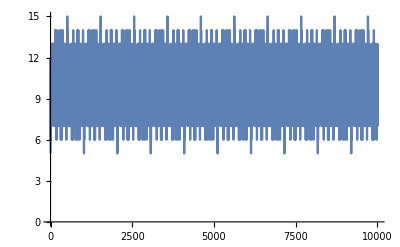

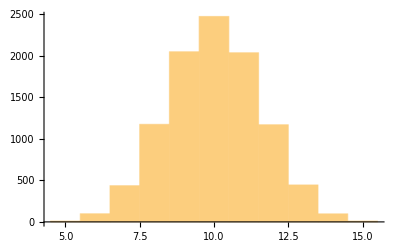

```mathematica
long = 1.5;
short = 0.5;
Clear[trial];
trial =RodEvolution[interesting[[4]],10,1000]; (*Working with a 10 rod example*)
trail
rodstates = trail[[All,2;;-2]];(*throw away the boundary conditions as they are not physical rods*)
rodstates
Dimensions[rodstates]
rodlengths = rodstates/. {1->long,0->short};(*exchange on and off with actual rod lengths*)
rodlengths
 travel = Total[rodlengths,{2}]; (*Caluclate the total length of the rod asssembly at a given state*)
ListLinePlot[travel] (*Sum accross rows, first replace 2 with fixed condion*)
Histogram[travel]
```

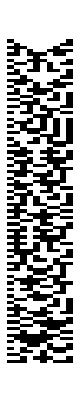
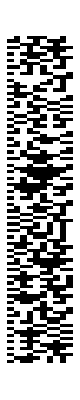
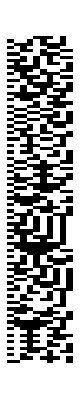
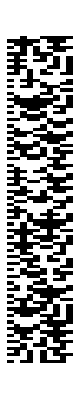
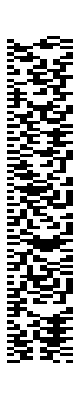
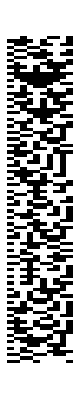
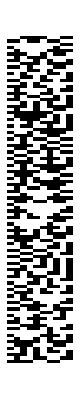
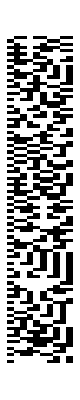

```mathematica
ArrayPlot/@Partition[rodstates,100]
```

```mathematica
GraphSingleRod[startloc_,onof_]:={Line[{{startloc,1},{If[onof==1,long,short]+startloc,1}},VertexColors->If[onof==1,{Green, Black},{Red, Black}]]};
```

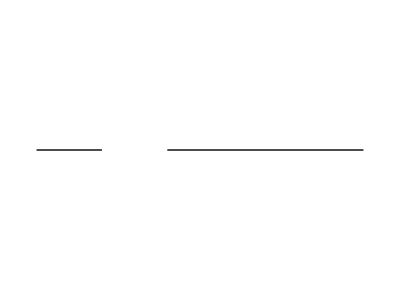

```mathematica
Graphics[{GraphSingleRod[0,0],GraphSingleRod[1,1]}]
```

```mathematica
rodstates[[5]]
rodlengths[[5]]
startlocs = Accumulate[rodlengths[[5]]]
```

{0,1.5,0,1.5,0,0,1.5,1.5,1.5,1.5}

{0.5,1.5,0.5,1.5,0.5,0.5,1.5,1.5,1.5,1.5}

{0.5,2.,2.5,4.,4.5,5.,6.5,8.,9.5,11.}

```mathematica
Length[startlocs]
```

10

```mathematica
Length[rodstates[[5]]]
```

10

```mathematica
Graphics[Table[GraphSingleRod[startlocs[[i]],examplestate[[i]]],{i,1,10}]]
```

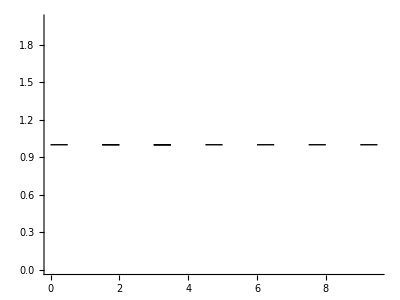

```mathematica
Show[Graphics[Table[GraphSingleRod[startlocs[[i]],examplestate[[i]]],{i,1,10}]],Axes->True]
```